```mathematica
f[x_]:=Sin[x+Cos[x]];
```

```mathematica
a=-1;b=3;h=0.2;
```

```mathematica
D1=Table[{i,(f[i+h]-f[i-h])/(2*h)},{i,a,b,h}]//N;
```

```mathematica
D1//TableForm
```

-1. | 0.711052
-0.8 | 0.41597
-0.6 | -1.13075
-0.4 | -0.527047
-0.2 | 1.10769
0. | 0.4276
0.2 | 0.0463707
0.4 | 0.283203
0.6 | -0.329449
0.8 | -0.118711
1. | -0.236963
1.2 | -0.498591
1.4 | 0.576031
1.6 | 0.242311
1.8 | 0.0172506
2. | -1.19877
2.2 | 0.00282127
2.4 | 0.845545
2.6 | -1.10382
2.8 | 0.712905
3. | 0.981881

```mathematica
dis[x_]=D[f[x],x]
```

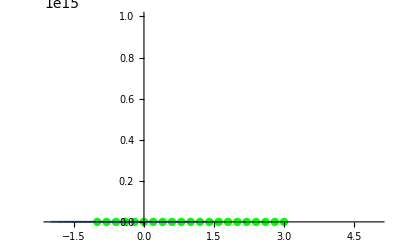

```mathematica
Show[ListPlot[D1,PlotStyle->{Green,PointSize[0.015]}],Plot[dis[x],{x,-2,4}],PlotRange->{{-2,5},{0,10^18}}]
```

```mathematica
Show[ListPlot[D1,PlotStyle->{Red,PointSize[0.015]}],Plot[dis[x],{x,-2,8}],PlotRange->{{-2,5},{0,5}}]
```

-Graphics-